```mathematica
(*гр.221703*)
(*Гаврилович Алиса*)
```

```mathematica
(*Лабораторная работа №3*)
```

```mathematica
(*Задание 1,при n = 6*)
```

```mathematica
(*пункт а*)
```

```mathematica
f[x_]:=√(x^3+4)*Cos[x/(√17)+1/21];(*функция согласно варианту*)
a=0;
b=6;
n=6;
h=(b-a)/n;(*шаг*)
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]];(*создаем таблицу аргументов и значений функции на отрезке[0,n],разделя отрезок на равные части*)
TableForm[data]
```

0. | 1.99773
1. | 2.1426
2. | 2.98413
3. | 3.97685
4. | 4.3315
5. | 3.4702
6. | 1.00729

```mathematica
u[i_]:=data[[i,2]]
v[i_]:=data[[i,1]]
Y=Array[u,n+1](*массив значений функции*)
X=Array[v,n+1](*массив аргументов*)
```

{1.99773,2.1426,2.98413,3.97685,4.3315,3.4702,1.00729}

{0.,1.,2.,3.,4.,5.,6.}

```mathematica
LagrangeInterpolation[X_,Y_,n_]:=∑_(i=1)^n Y[[i]]*Product[If[i!=j,(x-X[[j]])/(X[[i]]-X[[j]]),1],{j,1,Length[X]}];(*формула интерполяции Лагранжа*)
```

```mathematica
Ln=Simplify[LagrangeInterpolation[X,Y,n+1]](*многочлен Лагранжа*)
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

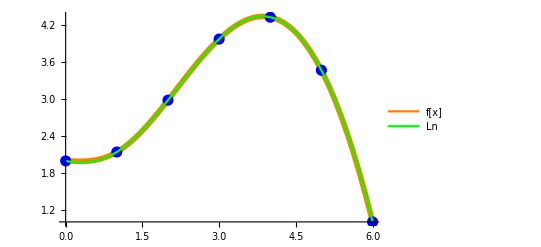

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Ln,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Ln"}]]
```

```mathematica
(*пункт б*)
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];(*массив для конечных разностей*)
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=""]];(*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
For[k=1,k<=n,k++,(*Считаем конечные разности*)
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{6,5}]  (*таблица конечных разностей*)
```

1.99773 |  0.14487 |  0.69666 | -0.54547 | -0.24378 |  0.45513 | -0.47422
 2.14260 |  0.84153 |  0.15119 | -0.78925 |  0.21135 | -0.01910 | 
 2.98413 |  0.99272 | -0.63806 | -0.57790 |  0.19226 |  | 
 3.97685 |  0.35466 | -1.21596 | -0.38564 |  |  | 
 4.33150 | -0.86131 | -1.60161 |  |  |  | 
 3.47020 | -2.46291 |  |  |  |  | 
 1.00729 |  |  |  |  |  |

```mathematica
(*пункт в*)
secNewtonInterpolation[X_,Y_,tab_,h_,n_]:=Y[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-X[[n]])/h+k-1))/Factorial[i]*tab[[n-i,i+1]]);(*вторая интерполяционная формула Ньютона*)
Pn=Simplify[secNewtonInterpolation[X,Y,tab,h,n+1]](*второй интерполяционный многочлен Ньютона*)
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

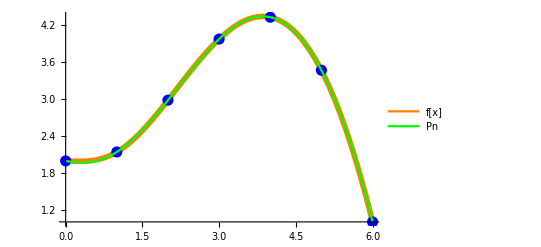

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Pn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Pn"}]]
```

```mathematica
(*пункт г*)
```

```mathematica
Npn[x_]=Simplify[InterpolatingPolynomial[data,x]](*интерполяционный многочлен Ньютона с помощью встроенной функции InterpolatingPolynomial**)
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

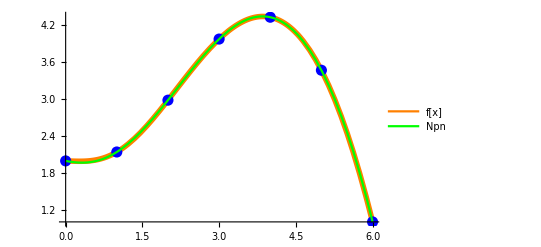

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Npn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Npn"}]]
```

```mathematica
(*пункт д*)
```

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Npn/.x->2.4316
```

3.44521

3.44199

3.44199

3.44199

```mathematica
(*пункт e*)
```

```mathematica
Rn[x_]=Abs[f[x]-Npn[x]];(*формула абсолютной погрешности интерполирования многочленом Ньютона*)
```

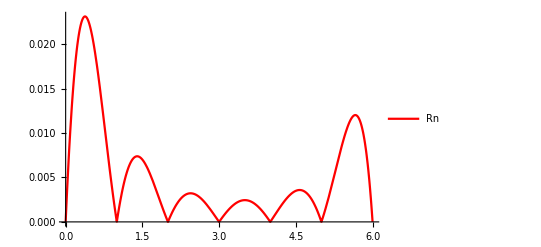

```mathematica
gr1=Plot[Rn,{x,a,b},PlotStyle->Red];
Legended[Show[gr1],LineLegend[{Red},{"Rn"}]]
```

```mathematica
FindMaximum[Rn[x],{x,0,n}](*максимум погрешности на отрезке [0,6]*)
```

{0.0231125,{x→0.378675}}

```mathematica
(*Задание 1,при n = 10*)
```

```mathematica
(*пункт а*)
```

```mathematica
f[x_]:=√(x^3+4)*Cos[x/(√17)+1/21];
a=0;
b=6;
n=10;
h=(b-a)/n;
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]];
TableForm[data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
u[i_]:=data[[i,2]]
v[i_]:=data[[i,1]]
Y=Array[u,n+1]
X=Array[v,n+1]
```

{1.99773,2.01511,2.25738,2.77518,3.4121,3.97685,4.30757,4.27163,3.76106,2.69216,1.00729}

{0.,0.6,1.2,1.8,2.4,3.,3.6,4.2,4.8,5.4,6.}

```mathematica
LagrangeInterpolation[X_,Y_,n_]:=∑_(i=1)^n Y[[i]]*Product[If[i!=j,(x-X[[j]])/(X[[i]]-X[[j]]),1],{j,1,Length[X]}];
```

```mathematica
Ln=Simplify[LagrangeInterpolation[data[[All,1]],data[[All,2]],n+1]]
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

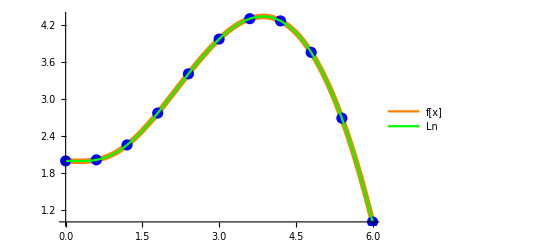

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Ln,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Ln"}]]
```

```mathematica
(*пункт б*)
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=""]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{6,5}]
```

1.99773 |  0.01738 |  0.22489 |  0.05063 | -0.20704 |  0.17214 | -0.10777 |  0.04314 |  0.01728 | -0.06941 |  0.11138
 2.01511 |  0.24227 |  0.27553 | -0.15640 | -0.03490 |  0.06436 | -0.06464 |  0.06041 | -0.05213 |  0.04198 | 
 2.25738 |  0.51780 |  0.11912 | -0.19130 |  0.02946 | -0.00027 | -0.00422 |  0.00829 | -0.01015 |  | 
 2.77518 |  0.63692 | -0.07218 | -0.16184 |  0.02919 | -0.00450 |  0.00406 | -0.00186 |  |  | 
 3.41210 |  0.56474 | -0.23402 | -0.13265 |  0.02469 | -0.00043 |  0.00220 |  |  |  | 
 3.97685 |  0.33073 | -0.36667 | -0.10796 |  0.02426 |  0.00177 |  |  |  |  | 
 4.30757 | -0.03594 | -0.47463 | -0.08369 |  0.02603 |  |  |  |  |  | 
 4.27163 | -0.51057 | -0.55832 | -0.05766 |  |  |  |  |  |  | 
 3.76106 | -1.06889 | -0.61598 |  |  |  |  |  |  |  | 
 2.69216 | -1.68488 |  |  |  |  |  |  |  |  | 
 1.00729 |  |  |  |  |  |  |  |  |  |

```mathematica
(*пункт в*)
secNewtonInterpolation[X_,Y_,tab_,h_,n_]:=Y[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-X[[n]])/h+k-1))/Factorial[i]*tab[[n-i,i+1]]);
Pn=Simplify[secNewtonInterpolation[X,Y,tab,h,n+1]]
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

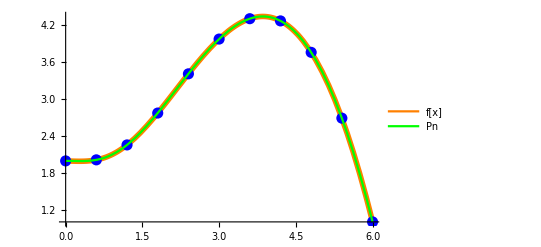

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Pn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Pn"}]]
```

```mathematica
(*пункт г*)
```

```mathematica
Npn[x_]=Simplify[InterpolatingPolynomial[data,x]]
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

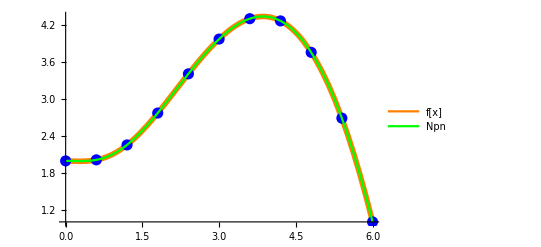

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Npn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Npn"}]]
```

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Npn/.x->2.4316
```

3.44521

3.44522

3.44522

3.44522

```mathematica
(*пункт e*)
```

```mathematica
Rn[x_]=Abs[f[x]-Npn[x]];
```

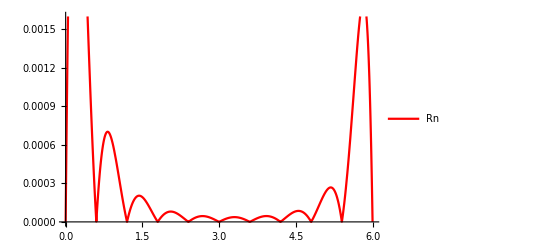

```mathematica
gr1=Plot[Rn[x],{x,a,b},PlotStyle->Red];
Legended[Show[gr1],LineLegend[{Red},{"Rn"}]]
```

```mathematica
Maximize[{Rn[x],a<=x<=b},x]
```

{0.00345993,{x→0.195904}}

```mathematica
(*пункт ж*)
(*Вывод:чем больше узлов(степень многочлена n), тем меньше погрешность*)
```

```mathematica
(*Задание 2*)
(*при n=6*)
(*пункт а*)
a=0;
b=6;
n=6;
t[i_]:=Cos[(Pi*(2*i+1))/(2*n+2)];(*многочлен Чебышева*)
arg[i_]:=(a+b)/2+(b-a)/2*t[i];
```

```mathematica
data=N[Table[{arg[i],f[arg[i]]},{i,0,n}]];(*Считаем значения функции на отрезке[0,n] c неравноотстоящими точками*)
u[i_]:=data[[i,2]]
v[i_]:=data[[i,1]]
Y=Array[u,n+1];
X=Array[v,n+1];
TableForm[data]
```

5.92478 | 1.25356
5.34549 | 2.81403
4.30165 | 4.22113
3. | 3.97685
1.69835 | 2.67361
0.654506 | 2.02501
0.0752163 | 1.99577

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=""]];(*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
For[k=1,k<=n,k++,(*Считаем разделенные разности*)
For[i=0,i<=n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(data⟦i+k+1,1⟧-data⟦i+1,1⟧);]]
PaddedForm[TableForm[tab],{6,5}]  (*таблицa разделенных разностей*)
```

1.25356 | -2.69376 | -0.82912 | -0.05962 |  0.00809 |  0.00007 | -0.00074
 2.81403 | -1.34800 | -0.65473 | -0.09383 |  0.00773 |  0.00439 | 
 4.22113 |  0.18767 | -0.31251 | -0.13009 | -0.01543 |  | 
 3.97685 |  1.00122 |  0.16195 | -0.06488 |  |  | 
 2.67361 |  0.62136 |  0.35171 |  |  |  | 
 2.02501 |  0.05048 |  |  |  |  | 
 1.99577 |  |  |  |  |  |

```mathematica
(*пункт б*)
```

```mathematica
difResult=Table[dif[i,k],{i,0,n},{k,1,n}];(*таблица разностей без первого столбца*)
(*Интерполяционная формула Ньютона для неравноотстоящих узлов*)
```

```mathematica
NewtonDividedDifference[X_,Y_,n_,dif_]:=Y[[1]]+∑_(i=1)^n dif[[1,i]]*∏_(j=1)^i (x-X[[j]])(*формула интерполирования Ньютона для  неравноотстоящих узлов*)
```

```mathematica
Pnrn=Simplify[NewtonDividedDifference[X,Y,n,difResult]]
```

2.00184-0.0841559 x+0.0234692 x^2+0.3155 x^3-0.120241 x^4+0.0155404 x^5-0.000739371 x^6

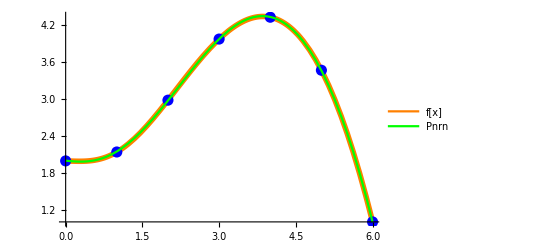

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Pnrn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Pnrn"}]]
```

```mathematica
(*пункт в*)
```

```mathematica
Intfn=Interpolation[data];(*интерполирующая функция с помощью встроенной команды Interpolation*)
```

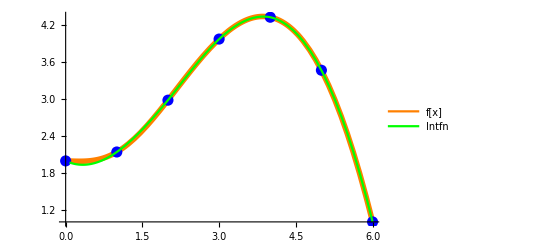

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Intfn[x],{x,X[[n+1]],b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Intfn"}]]
```

```mathematica
(*пункт г*)
```

```mathematica
f[2.4316]
Pnrn/.x->2.4316
Intfn[2.4316]
```

3.44521

3.43661

3.43661

```mathematica
(*пункт д*)
```

```mathematica
Rn1[x_]:=Abs[f[x]-Pnrn];(* асболютная погрешность интерполирования многочленoм Ньютона*)
```

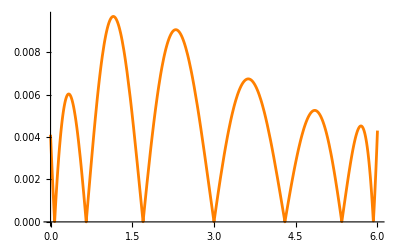

```mathematica
gr1=Plot[Rn1[x],{x,a,b},PlotStyle->{Orange,Thickness[0.005]}]
```

```mathematica
Maximize[{Rn1[x],a<=x<=b},x](*максимум погрешности*)
```

{0.00967787,{x→1.15209}}

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

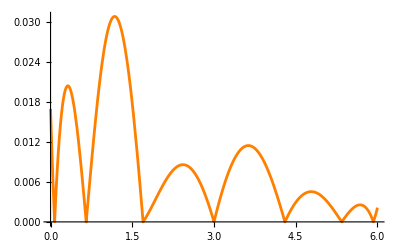

```mathematica
Rn2[x_]:=Abs[f[x]-Intfn[x]];(* асболютная погрешность интерполирования функцией Interpolation*)
gr2=Plot[Rn2[x],{x,a,b},PlotStyle->{Orange,Thickness[0.005]}]
```

```mathematica
Maximize[{Rn2[x],a<=x<=b},x](*максимум погрешности*)
```

InterpolatingFunction::dmval: Input value {0.030654} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.93434} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0692316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.0308731,{x→1.1767}}

```mathematica
(*при n=10*)
```

```mathematica
(*пункт а*)
a=0;
b=6;
n=10;
t[i_]:=Cos[(Pi*(2*i+1))/(2*n+2)];
arg[i_]:=(a+b)/2+(b-a)/2*t[i];
```

```mathematica
data=N[Table[{arg[i],f[arg[i]]},{i,0,n}]];
u[i_]:=data[[i,2]]
v[i_]:=data[[i,1]]
Y=Array[u,n+1];
X=Array[v,n+1];
TableForm[data]
```

5.96946 | 1.10849
5.7289 | 1.84742
5.26725 | 2.98013
4.62192 | 3.96756
3.8452 | 4.34385
3. | 3.97685
2.1548 | 3.15021
1.37808 | 2.3871
0.732751 | 2.04306
0.271104 | 1.9921
0.0305357 | 1.99698

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=""]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];

For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(data⟦i+k+1,1⟧-data⟦i+1,1⟧);]]
PaddedForm[TableForm[tab],{6,5}]
```

1.10849 | -3.07159 | -0.88003 | -0.03397 |  0.00873 |  0.00023 |  0.00005 | -8.17152×10^-6 | -0.00002 |  6.14019×10^-6 |  6.64259×10^-6
 1.84742 | -2.45362 | -0.83425 | -0.05252 |  0.00806 |  0.00004 |  0.00009 |  0.00010 | -0.00006 | -0.00003 | 
 2.98013 | -1.53013 | -0.73532 | -0.07450 |  0.00793 | -0.00035 | -0.00040 |  0.00040 |  0.00013 |  | 
 3.96756 | -0.48446 | -0.56641 | -0.09918 |  0.00928 |  0.00146 | -0.00239 | -0.00031 |  |  | 
 4.34385 |  0.43422 | -0.32171 | -0.12930 |  0.00362 |  0.01184 | -0.00098 |  |  |  | 
 3.97685 |  0.97805 | -0.00272 | -0.14057 | -0.03869 |  0.01556 |  |  |  |  | 
 3.15021 |  0.98246 |  0.31598 | -0.03499 | -0.08489 |  |  |  |  |  | 
 2.38710 |  0.53313 |  0.38189 |  0.14533 |  |  |  |  |  |  | 
 2.04306 |  0.11038 |  0.18605 |  |  |  |  |  |  |  | 
 1.99210 | -0.02027 |  |  |  |  |  |  |  |  | 
 1.99698 |  |  |  |  |  |  |  |  |  |

```mathematica
(*пункт б*)
```

```mathematica
difResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
NewtonDividedDifference[X_,Y_,n_,dif_]:=Y[[1]]+∑_(i=1)^n dif[[1,i]]*∏_(k=1)^i (x-X[[k]])
```

```mathematica
Pnrn=Simplify[NewtonDividedDifference[X,Y,n,difResult]]
```

1.99777-0.024875 x-0.0365212 x^2+0.145948 x^3+0.213497 x^4-0.228116 x^5+0.0941137 x^6-0.0215967 x^7+0.00289609 x^8-0.000212863 x^9+6.64259×10^-6 x^10

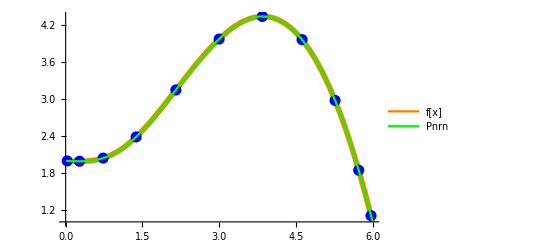

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Pnrn,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Pnrn"}]]
```

```mathematica
(*пункт в*)
```

```mathematica
Intfn=Interpolation[data];
```

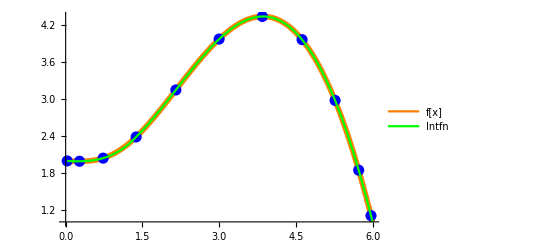

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Intfn[x],{x,X[[n+1]],b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Intfn"}]]
```

```mathematica
f[2.4316]
Pnrn/.x->2.4316
Intfn[2.4316]
```

3.44521

3.44556

3.44279

```mathematica
Rn1[x_]=Abs[f[x]-Pnrn];
```

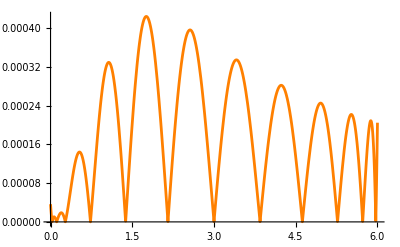

```mathematica
gr1=Plot[Rn1[x],{x,a,b},PlotStyle->{Orange,Thickness[0.005]}];
Show[gr1]
```

```mathematica
Maximize[{Rn1[x],a<=x<=b},x](*максимум погрешности*)
```

{0.000424027,{x→1.75748}}

```mathematica
Rn2[x_]=Abs[f[x]-Intfn[x]];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

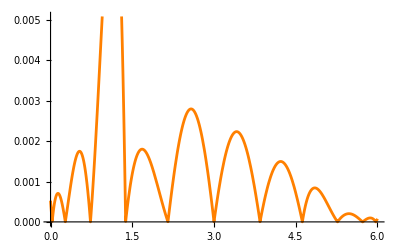

```mathematica
gr2=Plot[Rn2[x],{x,a,b},PlotStyle->{Orange,Thickness[0.005]}];
Show[gr2]
```

```mathematica
Maximize[{Rn2[x],a<=x<=b},x](*максимум погрешности*)
```

{0.00849155,{x→1.15493}}

```mathematica
(*Задание 3*)
(*Вывод:чем больше узлов,тем меньше погрешность интерполирования;это также можно наблюдать на графиках,где при большом количестве узлов функции сильнее накладываются друг на друга *)

(*Задание 4*)
a=0;
b=6;
n=10;
h=(b-a)/n;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]];
TableForm[data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
(*пункт a*)
(*задание не получилось,не подключается пакет(?)*)
Needs["Splines`"]
S3=SplineFit[data,Cubic]
SplineFunction[Cubic,{0.,6.},<>];
gr1=ParametricPlot[S3[x],{x,a,b}];
Show[gr1]
```

```mathematica
(*пункт б*)
```

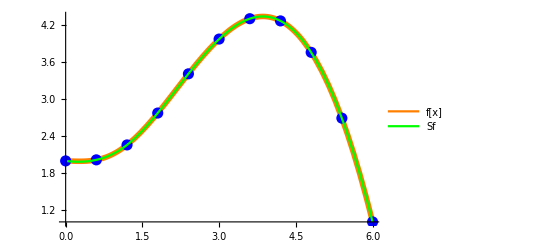

```mathematica
Sf=Interpolation[data,Method->"Spline"];(*интерполяция сплайном Sf (x) с помощью функции Interpolation*)
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[S3[x],{x,X[[n+1]],b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Sf"}]]
```

```mathematica
(*пункт в*)
```

```mathematica
f[2.4316]
Sf[2.4316]
```

3.44521

3.44519

```mathematica
(*Задание 5*)
(*пункт а*)
a=0;
b=6;
n=10;
h=(b-a)/n;m=1;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]];
TableForm[data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
u[i_]:=data[[i,2]]
v[i_]:=data[[i,1]]
Y=Array[u,n+1];
X=Array[v,n+1];
a11=n;(*коэффициенты системы уравнений методом наименьших квадаратов kx+b*)
a12=∑_(i=1)^(n+1) data⟦i,1⟧;
a21=a12;
a22=∑_(i=1)^(n+1) (data⟦i,1⟧)^2;
b1=∑_(i=1)^(n+1) data⟦i,2⟧;
b2=∑_(i=1)^(n+1) (data⟦i,1⟧*data[[i,2]]);
A=({{a11, a12}, {a21, a22}});
B=({{b1}, {b2}});
k=LinearSolve[A,B];(*коэффициенты найдены*)
Q1[x_]=k[[2]]*x+k[[1]](*результат апроксимации функции многочленом первой степени*)
```

{3.91952-0.203671 x}

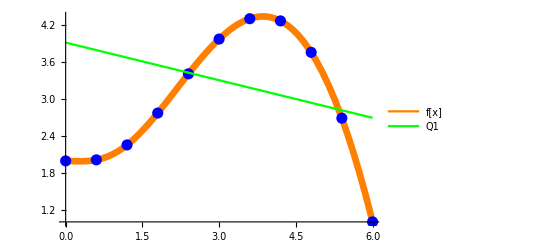

```mathematica
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.012]}];
gr2=Plot[Q1[x],{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Q1"}]]
```

{2.8598+0.679425 x-0.133802 x^2}

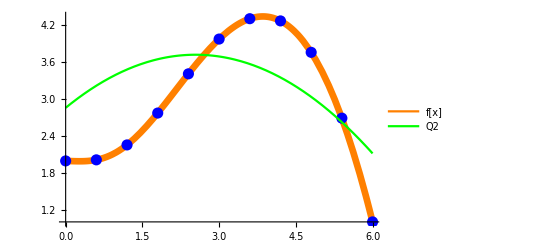

```mathematica
(*пункт б*)

a13=a22;(*коэффициенты системы уравнений методом наименьших квадаратов kx^2+bx+c*)
a23=∑_(i=1)^(n+1) (data⟦i,1⟧)^3;
a31=a22;
a32=a23;
a33=∑_(i=1)^(n+1) (data⟦i,1⟧)^4;
b3=∑_(i=1)^(n+1) (data⟦i,1⟧^2*data[[i,2]]);
A=({{a11, a12, a13}, {a21, a22, a23}, {a31, a32, a33}});
B=({{b1}, {b2}, {b3}});
k=LinearSolve[A,B];(*коэффициенты найдены*)
Q2[x_]=k[[3]]*x^2+k[[2]]*x+k[[1]](*результат апроксимации функции многочленом второй степени*)
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.012]}];
gr2=Plot[Q2[x],{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Q2"}]]
```

```mathematica
(*пункт в*)
```

1.9958-0.378264 x+0.648479 x^2-0.102351 x^3

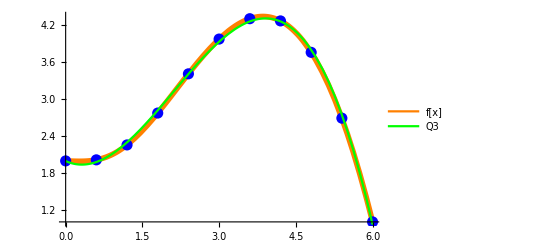

```mathematica
Q3=Fit[data,{1,x,x^2,x^3},x](*многочлен наилучшего среднеквадратичного приближения третьей степени с использованием функции Fit *)
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Q3,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Q3"}]]
```

2.02452-0.544448 x+0.786966 x^2-0.139281 x^3+0.00307748 x^4

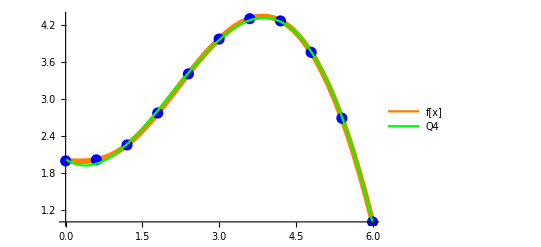

```mathematica
Q4=Fit[data,{1,x,x^2,x^3,x^4},x]
(*многочлен наилучшего среднеквадратичного приближения четвертой степени с использованием функции Fit *)
gr1=Plot[f[x],{x,a,b},PlotStyle->{Orange,Thickness[0.01]}];
gr2=Plot[Q4,{x,a,b},PlotStyle->Green];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[gr1,points,gr2],LineLegend[{Orange,Green},{"f[x]","Q4"}]]
```

```mathematica
(*пункт г*)
```

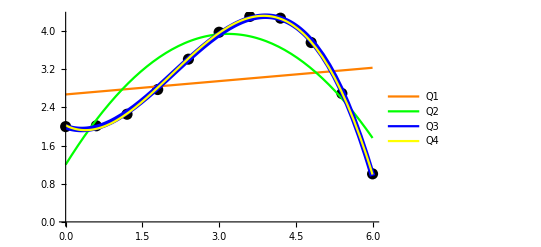

```mathematica
gr1=Plot[Q1,{x,a,b},PlotStyle->Orange];
gr2=Plot[Q2,{x,a,b},PlotStyle->Green];
gr3=Plot[Q3,{x,a,b},PlotStyle->{Blue,Thickness[0.01]}];
gr4=Plot[Q4,{x,a,b},PlotStyle->Yellow];
points=ListPlot[data,PlotStyle->{PointSize[0.02],Black}];
Legended[Show[points,gr1,gr2,gr3,gr4],LineLegend[{Orange,Green,Blue,Yellow},{"Q1","Q2","Q3","Q4"}]]
```